# Practical 7

## Plotting The characteristic equations of partial differential equation

### 1. xu_x + yu_y = u The characteristic equations are given by :- dx/x= dy/y=du/u on solving above system, we get ξ = c_1 = y/x or y = xc_1 η = c_2 = u/y or u = yc_2 where c1 and c2 are arbitrary constants

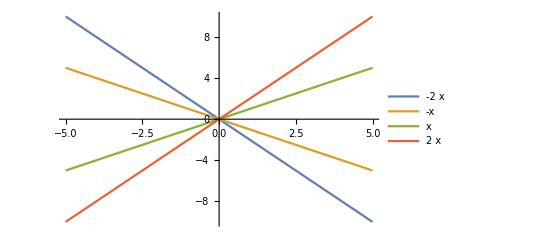

```mathematica
Plot[{-2x, -1x, x, 2x}, {x, -5, 5}, PlotLegends->{-2x, -1x, x, 2x}]
```

```mathematica
Plot3D[{-2y, -y, y, 2y},{x, -5, 5}, {y,-5, 5}, Mesh->None, PlotStyle->Opacity[0.6], PlotLegends->{-2y, -y, y, 2y}]
```

-Graphics3D-

### 2. u_x - u_y = 1 The characteristic equations are given by :- dx/1= -dy/1=du/1 on solving above system, we get ξ = c_1 = y+x or y = c_1-x η = c_2 = u-x or u = x + c_2 where c1 and c2 are arbitrary constants

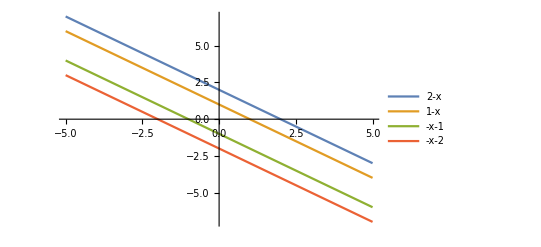

```mathematica
Plot[{2-x, 1-x, -1-x, -2-x}, {x, -5, 5}, PlotLegends->{2-x, 1-x, -1-x, -2-x}]
```

```mathematica
Plot3D[{x + 2, x + 1, x - 1, x -2},{x, -5, 5}, {y,-5, 5}, Mesh->None, PlotStyle->Opacity[0.6], PlotLegends->{x + 2, x + 1, x - 1, x -2}]
```

-Graphics3D-

### 3. yu_x + xu_y = u The characteristic equations are given by :- dx/y= dy/x=du/u on solving above system, we get ξ = c_1 = y^2-x^2 or y = ±√(c_1+x^2) η = c_2 = (x+y)/u or u = (x + y)/c_2 where c1 and c2 are arbitrary constants

```mathematica
eqns = Join[Table[Sqrt[c + x^2], {c, -1, 1}], Table[-Sqrt[c + x^2], {c, -1, 1}]]
```

{√(-1+x^2),√(x^2),√(1+x^2),-√(-1+x^2),-√(x^2),-√(1+x^2)}

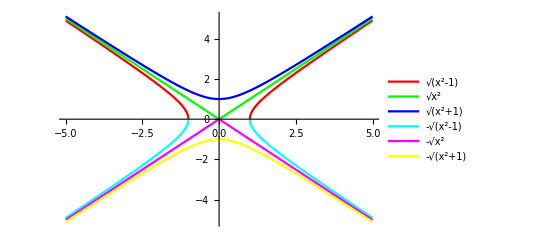

```mathematica
Plot[eqns, {x, -5, 5}, PlotLegends->eqns, PlotStyle->{Red, Green, Blue, Cyan, Magenta, Yellow}]
```

```mathematica
eqns3d = Table[If[c != 0, (x + y)/c, ## &[]], {c, -2, 2}]
```

{1/2 (-x-y),-x-y,x+y,(x+y)/2}

```mathematica
Plot3D[eqns3d,{x, -5, 5}, {y,-5, 5}, Mesh->None, PlotStyle->Opacity[0.6], PlotLegends->eqns3d]
```

-Graphics3D-

### 4. x y u_x + (x^2+y^2)u_y = 0 The characteristic equations are given by :- dx/(x y)= dy/(x^2+y^2)=du/0 on solving above system, we get ξ = c_1 = u or u = c_1 η = c_2 = (y^2-x^2)/x or y^2 = x c_2 + x^2 where c1 and c2 are arbitrary constants

```mathematica
eqns = Table[x*c + x^2, {c, -1, 1}]
```

{-x+x^2,x^2,x+x^2}

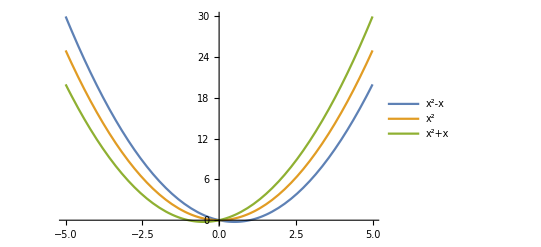

```mathematica
Plot[eqns, {x, -5, 5}, PlotLegends->eqns]
```

```mathematica
eqns3d = Table[c, {c, -1, 1}]
```

{-1,0,1}

```mathematica
Plot3D[eqns3d, {x, -5, 5}, {y, -5, 5}, PlotLegends->eqns,Mesh->None, PlotStyle->Opacity[0.6]]
```

-Graphics3D-

### 5. (u - y) u_x + y u_y = x + y The characteristic equations are given by :- dx/(u-y)= dy/y=du/(x+y) on solving above system, we get ξ = c_1 = (x+u)/y or u = y c_1-x η = c_2 = (x + y)^2 - u^2 or u = ±√((x + y)^2-c_2) where c1 and c2 are arbitrary constants

```mathematica
eqns3d = Table[y*c - x, {c, -1, 1}]
```

{-x-y,-x,-x+y}

```mathematica
Plot3D[eqns3d, {x, -5, 5}, {y, -5, 5}, PlotLegends->eqns,Mesh->None, PlotStyle->Opacity[0.6]]
```

-Graphics3D-

```mathematica
eqns3d = Join[Table[Sqrt[(x + y)^2-c], {c, -1, 1}], Table[-Sqrt[(x + y)^2-c], {c, -1, 1}]]
```

{√(1+(x+y)^2),√((x+y)^2),√(-1+(x+y)^2),-√(1+(x+y)^2),-√((x+y)^2),-√(-1+(x+y)^2)}

```mathematica
Plot3D[eqns3d,{x, -1, 1}, {y,-1, 1}, Mesh->None, PlotStyle->{{Red, Opacity[0.6]}, {Green, Opacity[0.6]}, {Blue, Opacity[0.6]}, {Cyan, Opacity[0.6]}, {Magenta, Opacity[0.6]}, {Yellow, Opacity[0.6]}}, PlotLegends->eqns3d ]
```

-Graphics3D-